```mathematica
SetDirectory[NotebookDirectory[]];
silver=<|"Date"->#1,"Value"->#2|>&@@@Import["quote-download/XAG.csv", "Table"]//Rest;
decisionsRawWithSchema=Import["ag-lm-1.csv", "Data"];
(*With[{dates=First/@silver, n=Length@silver}, Transpose[{dates,  RandomReal[{-5,5}, n],RandomReal[{0.25,10}, n]}]];
First/@silver ==First/@decisions*)
binaryDecisionsRawWithSchema=Import["lasso-binary-ag-1.csv", "Data"];
```

```mathematica
decisionsRawWithSchema[[1]]
```

{,as.Date(dates[783:804]),ex/100,upper/100,lower/100,actuals/100}

```mathematica
binaryDecisionsRawWithSchema[[1]]
```

{,dates.585.805.,as.vector.pr.,as.vector.pred...1..,as.vector.pred...2..}

```mathematica
decisionsRaw=Rest@decisionsRawWithSchema;
binaryRaw=Rest@binaryDecisionsRawWithSchema;
logNormalVar[mu_,var_]:=(Exp[var]-1)Exp[2mu+var];
decisions=With[{dates=decisionsRaw[[All,2]],meanLogReturns=decisionsRaw[[All,3]],varLogReturns=((decisionsRaw[[All,4]]-decisionsRaw[[All,5]])/(2*2 (*95% ci*)))^2},<|"Date"->#1,"Return"->#2,"Var"->#3|>&@@@Transpose@{dates,Exp[meanLogReturns]-1,MapThread[logNormalVar,{meanLogReturns,varLogReturns}]}];
binary=<|"Date"->#1,"Buy"->#2|>&@@@binaryRaw;
```

```mathematica
joined=JoinAcross[decisions, silver,Key["Date"],"Left"];
joinedBin=JoinAcross[binary, silver,Key["Date"],"Left"];
```

```mathematica
Length@joined
Length@joinedBin
```

22

221

```mathematica
invest=1000000;
makeInvestment[{money_,ownedCommodities_}, {leverage_, currPrice_}]:=With[{toSell=ownedCommodities*currPrice},With[{newMoney=money+toSell},
With[{toSpend=newMoney*leverage},
With[{newCommodities=toSpend/currPrice},
{newMoney-toSpend, newCommodities}]]]]
state=FoldList[makeInvestment, {invest,0}, {#["Return"]/#["Var"],#["Value"]}&/@joined];
prices=Prepend[#["Value"]&/@joined,First[joined]["Value"]];
value=First/@state+Last/@state*prices;
```

```mathematica
boolSgn[x_]:=If[x, 1, -1]
```

```mathematica
makeInvestmentBinAvg[{money_,ownedCommodities_,oldEdge_,n_,lastPrice_,lastBet_(*direction, via sign, of last bet, 1 = buy, -1 = short*)},currPrice_]:=
With[{runningEdge=(oldEdge *n+lastBet*boolSgn[lastPrice<currPrice])/(n+1),toSell=ownedCommodities*currPrice},With[{newMoney=money+toSell},
With[{toSpend=newMoney*runningEdge (*assume 1:1 odds*)},
With[{newCommodities=toSpend/currPrice},
{newMoney-toSpend, newCommodities,runningEdge,n+1,currPrice,boolSgn[toSpend>0]}]]]]
stateBin=FoldList[makeInvestmentBinAvg,{invest, 0, 0.5,0,0,0},#["Value"]&/@joinedBin];
pricesBin=Prepend[#["Value"]&/@joined,First[joined]["Value"]];
valueBin=First/@state+Last/@state*prices;
```

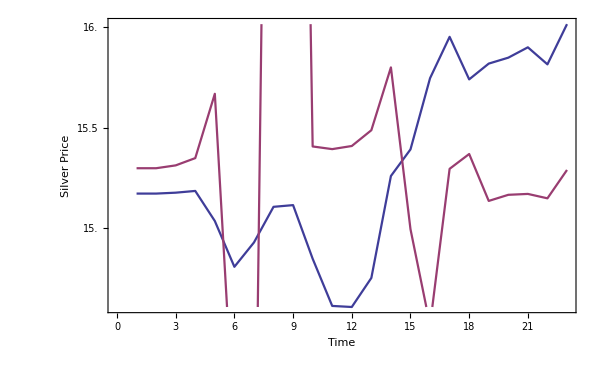
-Graphics-Ag PriceNet ValueTime

```mathematica
Labeled[Labeled[Labeled[TwoAxisListPlot[{prices,value},{{Joined->True,ImageSize->600,AxesLabel->{"Time","Silver Price"}}, {Joined->True,ImageSize->600,AxesLabel->{"Time", "Net Value"}}}],"Ag Price", Left],"Net Value", Right],"Time", Bottom]
```

```mathematica
Last@value-10^6
```

-93281.7

```mathematica
(* Two axis list plot adopted from docs *)
TwoAxisListPlot[{f_, g_}]:=TwoAxisListPlot[{f, g}, {{},{}}]
TwoAxisListPlot[{f_,g_},{{opts1___}, {opts2___}}, rTickAcc_Integer:4]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks,fstyle, gstyle},
(*Extract plot style*)
fstyle = Sequence@@Cases[{opts1}, (PlotStyle->a_):>a];
gstyle = Sequence@@Cases[{opts2}, (PlotStyle->a_):>a];
fgraph=ListPlot[f,Axes->True,PlotStyle->{ColorData[1][1], fstyle}, opts1];
ggraph=ListPlot[g,Axes->True,PlotStyle->{ColorData[1][2], gstyle}, opts2];
{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];gticks=N@Quiet@Transpose@{fticks,ToString[NumberForm[#,rTickAcc],StandardForm]&/@Rescale[fticks,frange,grange]};Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```